{a→7.29917,b→-135.189}

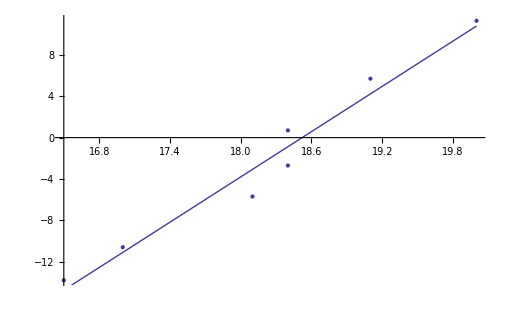

```mathematica
(*most data points are +/-.2 G, a few are +/-.1 G*)
d = {18.6,18.4,18.1,17,16.5,18.4,19.1,20.0};
B = {0,-2.7,-5.7,-10.6,-13.8,0.7,5.7,11.3};
data=Thread[{d,B}];
fitfn=a x + b;
fit = FindFit[data,fitfn,{a,b},x]
Show[{ListPlot[data[[2;;]]],
Plot[fitfn/.fit,{x,0,20}]
}]
```